```mathematica
ClearAll["Global`*"]
```

```mathematica
table051 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_1.txt",{"Table", "Data"}];
table051[[All,1]]=table051[[All,1]]-table051[[1,1]];
table051[[All,2]]=((table051[[All,2]]+0.002)/(0.0043×0.02408));
table051[[All,2]]=table051[[All,2]]-Min[table051[[All,2]]];
```

```mathematica
table052 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_2.txt",{"Table", "Data"}];
table052[[All,1]]=table052[[All,1]]-table052[[1,1]];
table052[[All,2]]=((table052[[All,2]]+0.002)/(0.0043×0.02408));
table052[[All,2]]=table052[[All,2]]-Min[table052[[All,2]]];
```

```mathematica
table053 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_3.txt",{"Table", "Data"}];
table053[[All,1]]=table053[[All,1]]-table053[[1,1]];
table053[[All,2]]=((table053[[All,2]]+0.002)/(0.0043×0.02408));
table053[[All,2]]=table053[[All,2]]-Min[table053[[All,2]]];
```

```mathematica
table054 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_4.txt",{"Table", "Data"}];
table054[[All,1]]=table054[[All,1]]-table054[[1,1]];
table054[[All,2]]=((table054[[All,2]]+0.002)/(0.0043×0.02408));
table054[[All,2]]=table054[[All,2]]-Min[table054[[All,2]]];
```

```mathematica
table055 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,5_5.txt",{"Table", "Data"}];
table055[[All,1]]=table055[[All,1]]-table055[[1,1]];
table055[[All,2]]=((table055[[All,2]]+0.002)/(0.0043×0.02408));
table055[[All,2]]=table055[[All,2]]-Min[table055[[All,2]]];
```

```mathematica
Export["table051.dat",table051];Export["table052.dat",table052];Export["table053.dat",table053];Export["table054.dat",table054];Export["table055.dat",table055];
```

```mathematica
T[k_,T0_,Tout_,t_]:=Tout+(T0-Tout)×Exp[-k×t]
```

```mathematica
fit051=FindFit[table051,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.20455,T0→18.1205,Tout→-2.70203}

```mathematica
fit052=FindFit[table052,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.179018,T0→19.3645,Tout→-4.00021}

```mathematica
fit053=FindFit[table053,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.192406,T0→19.4988,Tout→-0.183262}

```mathematica
fit054=FindFit[table054,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.18812,T0→23.9585,Tout→-0.0672191}

```mathematica
fit055=FindFit[table055,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.165685,T0→23.2323,Tout→-0.597109}

```mathematica
Tset=
```

```mathematica
k051=Mean[{k/.fit051,k/.fit052,k/.fit053,k/.fit054,k/.fit055}]
```

0.185955

```mathematica
StandardDeviation[{k/.fit051,k/.fit052,k/.fit053,k/.fit054,k/.fit055}]
```

0.0145865

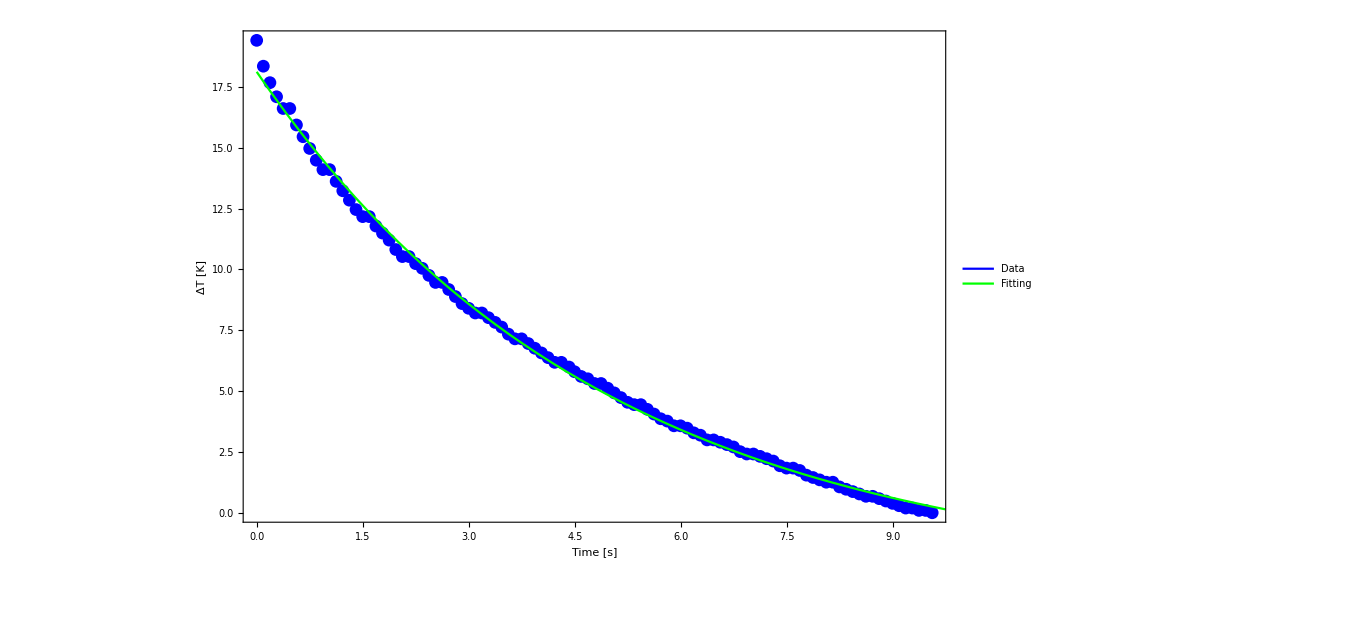

```mathematica
Legended[Show[ListPlot[table051,PlotStyle->Blue],
Plot[T[k,T0,Tout,t]/.fit051,{t,0,Max[table052[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Time [s]","ΔT [K]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```